```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

## n \mapsto t[n] is defined as a table in myFunctionsPureCodeV8 copy.nb, whhich is loaded by myFunctionsMathematica8.m. The table was created in my2ndEditOdlyzkoAccrtZrs6dec15.nb. It is from a table on Odlyzko’s site.

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

```mathematica
stream=OpenRead["zeta1fixedpts13dec15"];
ls=ReadList[stream];
Close[stream];
```

```mathematica
streem=OpenWrite["psiNrhoNspirals9mar16"]
```

OutputStream[psiNrhoNspirals9mar16,1748]

```mathematica
Close[streem]
```

psiNrhoNspirals9mar16

```mathematica
streem=OpenAppend["psiNrhoNspirals9mar16"];
precision=400;
For[n=0,n<10,n++;
fxx=ls[[n,2]];
zr=bestzero[n];
zeros={zr};
Write[streem,{n,1,zr}];
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision,WorkingPrecision->precision][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{n,k,zr}]];
Close[streem];
el=Length[zeros];
data={};
kla={};
jla={};
For[j=0,j<el,j++;
zr=zeros[[j]];
arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
jlap={j,la};
jla=Append[jla,jlap];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pj=ListPlot[data,Joined->True];
Print["N   ",n];
Print[Show[p,pj]]]
```

## leaf5point3r1c1:

N   1

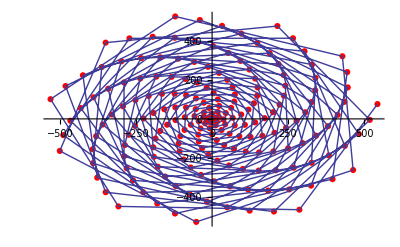

Write::noopen: Cannot open OutputStream["psiNrhoNspirals9mar16", 1750].

General::stop: Further output of Write :: noopen will be suppressed during this calculation.

General::openx: OutputStream["psiNrhoNspirals9mar16", 1750] is not open.

## leaf5point3r1c2:

N   2

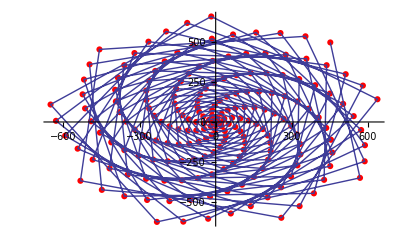

General::openx: OutputStream["psiNrhoNspirals9mar16", 1750] is not open.

## leaf5point3r2c1:

N   3

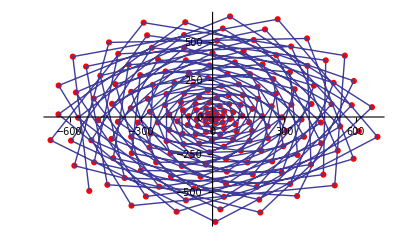

General::openx: OutputStream["psiNrhoNspirals9mar16", 1750] is not open.

General::stop: Further output of General :: openx will be suppressed during this calculation.

## leaf5point3r2c2

N   4

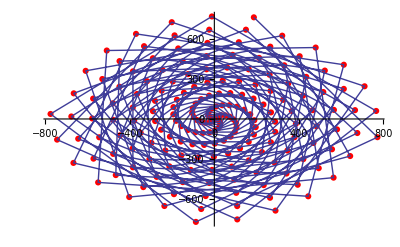

## leaf5point3r3c1

N   5

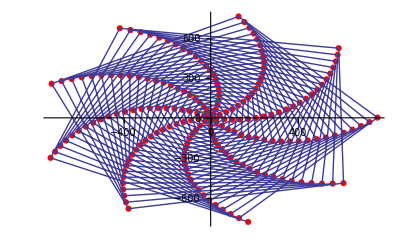

## leaf5point3r3c2

N   6

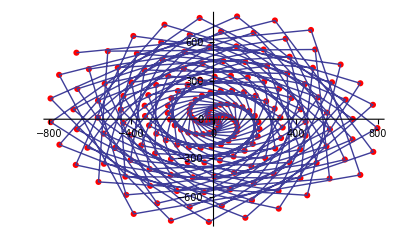

## leaf5point3r4c1

N   7

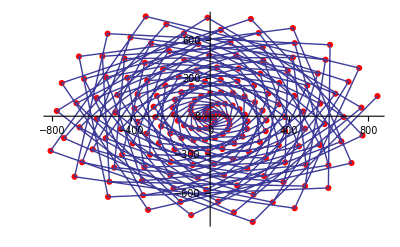

## leaf5point3r4c2

N   8

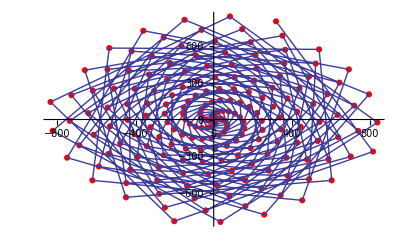

## leaf5point3r5c1

N   9

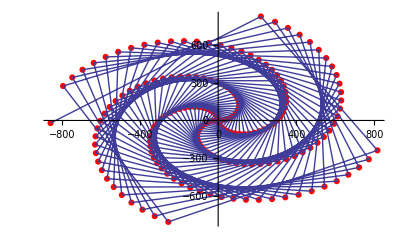

## leaf5point3r5c2

N   10